### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
Pin=Table[{RandomReal[10],RandomReal[10]},{i,10}](*Point input*)
```

{{9.87146,9.20622},{8.01204,7.24169},{9.88965,4.32722},{0.310577,3.839},{8.21031,6.70968},{4.46382,0.0129415},{1.06669,1.1388},{4.48217,7.79378},{2.40156,8.81868},{6.81364,7.87938}}

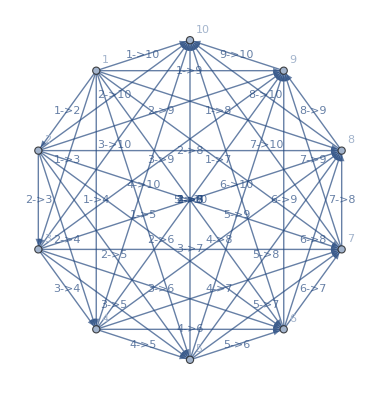

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"](*Ggraph input*)
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{2.70496,4.87903,10.9644,2.99868,10.6658,11.9418,5.5713,7.47994,3.33328,3.46692,8.41967,0.567749,8.05262,9.24571,3.57278,5.8279,1.3575,9.59151,2.91484,6.93201,9.3814,6.42323,8.73182,4.6989,8.40515,5.64695,2.80407,5.74826,5.40087,7.65601,7.6735,9.05903,3.88256,6.17976,1.82178,3.57882,7.78086,9.044,8.2099,7.48026,7.79503,8.85793,2.31934,2.33304,4.51095}

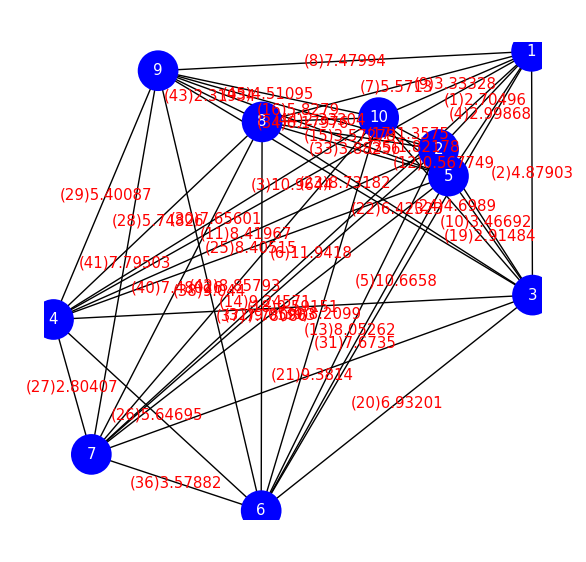

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[PD[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{2.70496,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,4.87903,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,10.9644,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,2.99868,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,10.6658,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,11.9418,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,5.5713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,7.47994,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,3.33328,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,3.46692,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.41967,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.567749,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.05262,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.24571,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.57278,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.8279,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.3575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.59151,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.91484,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.93201,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.3814,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.42323,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.73182,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.6989,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.40515,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.64695,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.80407,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.74826,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.40087,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.65601,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.6735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.05903,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.88256,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.17976,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82178,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.57882,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.78086,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.044,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.2099,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.48026,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.79503,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.85793,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.31934,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.33304,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.51095}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Point *)
```

{{{6.81364,7.87938},{9.87146,9.20622},{2.40156,8.81868}},{{6.81364,7.87938},{9.87146,9.20622},{4.48217,7.79378}},{{2.40156,8.81868},{9.87146,9.20622},{4.48217,7.79378}},{{6.81364,7.87938},{9.87146,9.20622},{1.06669,1.1388}},{{2.40156,8.81868},{9.87146,9.20622},{1.06669,1.1388}},{{4.48217,7.79378},{9.87146,9.20622},{1.06669,1.1388}},{{6.81364,7.87938},{9.87146,9.20622},{4.46382,0.0129415}},{{2.40156,8.81868},{9.87146,9.20622},{4.46382,0.0129415}},{{4.48217,7.79378},{9.87146,9.20622},{4.46382,0.0129415}},{{1.06669,1.1388},{9.87146,9.20622},{4.46382,0.0129415}},{{6.81364,7.87938},{9.87146,9.20622},{8.21031,6.70968}},{{2.40156,8.81868},{9.87146,9.20622},{8.21031,6.70968}},{{4.48217,7.79378},{9.87146,9.20622},{8.21031,6.70968}},{{1.06669,1.1388},{9.87146,9.20622},{8.21031,6.70968}},{{4.46382,0.0129415},{9.87146,9.20622},{8.21031,6.70968}},{{6.81364,7.87938},{9.87146,9.20622},{0.310577,3.839}},{{2.40156,8.81868},{9.87146,9.20622},{0.310577,3.839}},{{4.48217,7.79378},{9.87146,9.20622},{0.310577,3.839}},{{1.06669,1.1388},{9.87146,9.20622},{0.310577,3.839}},{{4.46382,0.0129415},{9.87146,9.20622},{0.310577,3.839}},{{8.21031,6.70968},{9.87146,9.20622},{0.310577,3.839}},{{6.81364,7.87938},{9.87146,9.20622},{9.88965,4.32722}},{{2.40156,8.81868},{9.87146,9.20622},{9.88965,4.32722}},{{4.48217,7.79378},{9.87146,9.20622},{9.88965,4.32722}},{{1.06669,1.1388},{9.87146,9.20622},{9.88965,4.32722}},{{4.46382,0.0129415},{9.87146,9.20622},{9.88965,4.32722}},{{8.21031,6.70968},{9.87146,9.20622},{9.88965,4.32722}},{{0.310577,3.839},{9.87146,9.20622},{9.88965,4.32722}},{{6.81364,7.87938},{9.87146,9.20622},{8.01204,7.24169}},{{2.40156,8.81868},{9.87146,9.20622},{8.01204,7.24169}},{{4.48217,7.79378},{9.87146,9.20622},{8.01204,7.24169}},{{1.06669,1.1388},{9.87146,9.20622},{8.01204,7.24169}},{{4.46382,0.0129415},{9.87146,9.20622},{8.01204,7.24169}},{{8.21031,6.70968},{9.87146,9.20622},{8.01204,7.24169}},{{0.310577,3.839},{9.87146,9.20622},{8.01204,7.24169}},{{9.88965,4.32722},{9.87146,9.20622},{8.01204,7.24169}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}](* 右回りならば負、左回りならば正 *)
```

{1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,-1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Area *)
```

{4.36315,1.41586,4.23108,6.49313,28.4253,15.5208,10.4682,33.2886,20.9536,18.6594,2.71494,9.00254,5.55413,4.2901,0.885518,1.86314,18.1937,7.71069,14.9373,29.4359,7.47665,7.47161,18.2263,13.16,21.5526,13.2756,4.07508,23.3726,1.77002,6.97712,3.98055,1.14825,3.23534,0.689362,4.40136,4.55392}

```mathematica
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}](* 誘導起電力は右回りなら負、左回りなら正 *)
```

{4.36315,1.41586,-4.23108,-6.49313,-28.4253,-15.5208,-10.4682,-33.2886,-20.9536,-18.6594,-2.71494,-9.00254,-5.55413,-4.2901,0.885518,-1.86314,-18.1937,-7.71069,14.9373,29.4359,7.47665,-7.47161,-18.2263,-13.16,-21.5526,-13.2756,-4.07508,-23.3726,-1.77002,-6.97712,-3.98055,-1.14825,3.23534,0.689362,-4.40136,4.55392}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.219581,-1.76455,0.550472,-0.525325,-1.10901,-0.203412,1.05557,1.56395,0.651878,-0.998407,0.26464,-0.514243,-0.993362,-0.322679,0.698142,0.912016,0.734312,-0.909941,1.01512,-2.37951,-1.63861,0.207089,0.238352,0.704537,-0.0159681,2.04922,2.30828,-1.3683,-2.32018,-0.747887,-1.22078,-0.567822,0.489896,0.691133,0.567156,-2.58747,-0.416955,-1.07937,0.430356,-0.963969,-1.83424,-0.213496,0.683945,-0.982474,-1.14438}

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{36,20,29,27,26,41,2,21,8,28,31,45,5,38,7,19,10,13,44,40,16,18,30,17,24,15,34,43,9,32,35,3,4,12,33,39,37,14,11,23,1,42,22,6,25}

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

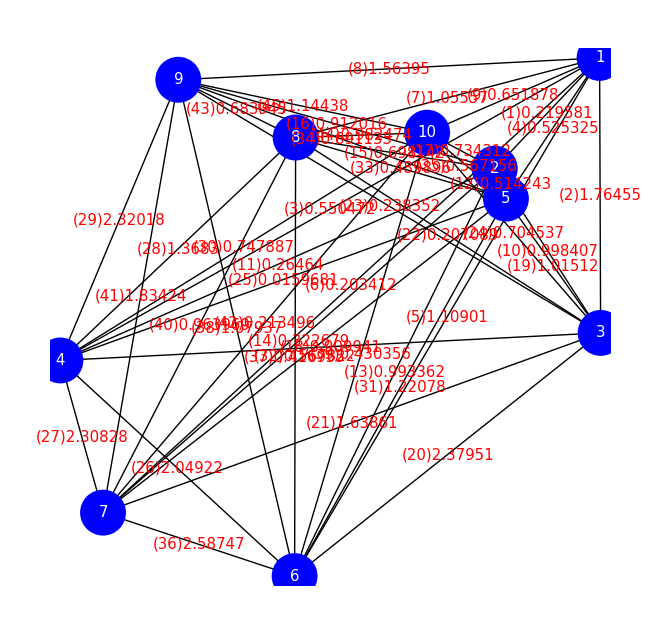

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
FindShortestTour[Pin]
```

{32.889,{1,2,5,3,6,7,4,9,8,10,1}}

```mathematica
FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[10]]]]]],
Infinity,All]
```

{{7->3,3->1,1->9,9->7},{6->3,3->1,1->9,9->4,4->6},{7->3,3->1,1->9,9->4,4->7},{7->6,6->3,3->1,1->9,9->7},{7->6,6->3,3->1,1->9,9->4,4->7}}

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
SortCurr=Reverse[Ordering[Abs[Curr]]]
```

{36,20,29,27,26,41,2,21,8,28,31,45,5,38,7,19,10,13,44,40,16,18,30,17,24,15,34,43,9,32,35,3,4,12,33,39,37,14,11,23,1,42,22,6,25}

```mathematica
MaxPartLoop={};
For[j=3,Length[MaxPartLoop]==0,j++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[j]]]]]],
Infinity,All];
]
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]]
```

{7→3,3→1,1→9,9→7}

```mathematica
PastEdgeList=MaxPartLoop
```

{7→3,3→1,1→9,9→7}

```mathematica
InsertPartLoop1=VertexInsertPartLoop[MaxPartLoop]
```

EdgeAdd::graph: EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]]の位置1にはグラフオブジェクトが想定されています．

EdgeAdd::graph: EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]の位置1にはグラフオブジェクトが想定されています．

EdgeRules::graph: EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]]の位置1にはグラフオブジェクトが想定されています．

EdgeAdd::graph: EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，EdgeAdd::graphのこれ以上の出力は表示されません．

EdgeRules::graph: EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，EdgeRules::graphのこれ以上の出力は表示されません．

Subgraph::graph: Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]の位置1にはグラフオブジェクトが想定されています．

EdgeDelete::graph: EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{«4»},ListPosRef[«3»]],{TriTourDiffTwoListMin[«1»],Rule[«2»]}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[«2»]],{DirectedEdge[«2»],DirectedEdge[«2»]}]],VertexList[]⟦1⟧→{3,6}]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]},ListPosRef[{},{},TriTourDiffTwoListMin[«1»]]],{TriTourDiffTwoListMin[{«4»}],3→6}]]]]]の位置1にはグラフオブジェクトが想定されています．

Subgraph::graph: Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，Subgraph::graphのこれ以上の出力は表示されません．

EdgeDelete::graph: EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{«4»},ListPosRef[«3»]],{TriTourDiffTwoListMin[«1»],Rule[«2»]}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[«2»]],{DirectedEdge[«2»],DirectedEdge[«2»]}]],VertexList[]⟦1⟧→{3,6}]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]},ListPosRef[{},{},TriTourDiffTwoListMin[«1»]]],{TriTourDiffTwoListMin[{«4»}],3→6}]]]]]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，EdgeDelete::graphのこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部EdgeRulesとListは等しいことが想定されています．

Union::heads: 位置3と1での頭部EdgeRulesとListは等しいことが想定されています．

Complement::heads: 位置2と1での頭部VertexListとListは等しいことが想定されています．

Union::heads: 位置2と1での頭部EdgeRulesとListは等しいことが想定されています．

General::stop: この計算中に，Union::headsのこれ以上の出力は表示されません．

Complement::heads: 位置2と1での頭部VertexListとListは等しいことが想定されています．

General::stop: この計算中に，Complement::headsのこれ以上の出力は表示されません．

EdgeDelete::inv: EdgeDelete[{7 -> 3, 3 -> 1, 1 -> 9, 9 -> 7}, ListPosRef[{7 -> 3, 3 -> 1}, {7 -> {3, 6}, {3, 6} -> 1}, TriTourDiffTwoListMin[{7 -> 3, 3 -> 1, 1 -> 9, 9 -> 7}]]]の引数ListPosRef[{7→3,3→1},{7→{3,6},{3,6}→1},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]は有効なedgeではありません．

EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{7→3,3→1},{7→{3,6},{3,6}→1},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],3→6}]]

```mathematica
PastEdgeList=Union[PastEdgeList,InsertPartLoop1]
```

Union::heads: 位置2と1での頭部EdgeRulesとListは等しいことが想定されています．

{7→3,3→1,1→9,9→7}∪EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]

```mathematica
InsertPartLoop2=VertexInsertPartLoop[InsertPartLoop1]
```

VertexList::graph: VertexList[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]の位置1にはグラフオブジェクトが想定されています．

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

VertexList::graph: VertexList[{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦1;;1⟧⟧]の位置1にはグラフオブジェクトが想定されています．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

VertexList::graph: …の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，VertexList::graphのこれ以上の出力は表示されません．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

Part::pkspec1: 式SortCurr⟦2⟧は部分指定に使用できません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Subgraph::graph: Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]の位置1にはグラフオブジェクトが想定されています．

Part::take: SortCurrの1から1の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

General::stop: この計算中に，Union::headsのこれ以上の出力は表示されません．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

General::stop: この計算中に，VertexList::argtのこれ以上の出力は表示されません．

Part::partw: VertexList[]の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Subgraph::graph: Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]の位置1にはグラフオブジェクトが想定されています．

EdgeDelete::graph: …の位置1にはグラフオブジェクトが想定されています．

EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]

```mathematica
PastEdgeList=Union[PastEdgeList,InsertPartLoop2]
```

Union::heads: 位置2と1での頭部EdgeRulesとListは等しいことが想定されています．

{7→3,3→1,1→9,9→7}∪EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]∪EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]

```mathematica
InsertPartLoop3=VertexInsertPartLoop[InsertPartLoop2]
```

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

VertexList::graph: VertexList[{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦1;;1⟧⟧]の位置1にはグラフオブジェクトが想定されています．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

VertexList::graph: VertexList[{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦1;;1⟧⟧]の位置1にはグラフオブジェクトが想定されています．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

Part::pkspec1: 式SortCurr⟦2⟧は部分指定に使用できません．

VertexList::graph: VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，VertexList::graphのこれ以上の出力は表示されません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Part::take: SortCurrの1から1の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

General::stop: この計算中に，Union::headsのこれ以上の出力は表示されません．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

General::stop: この計算中に，VertexList::argtのこれ以上の出力は表示されません．

Part::partw: VertexList[]の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]

```mathematica
PastEdgeList=Union[PastEdgeList,InsertPartLoop3]
```

Union::heads: 位置2と1での頭部EdgeRulesとListは等しいことが想定されています．

{7→3,3→1,1→9,9→7}∪EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]∪EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]∪EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],EdgeRules[VertexReplace[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->VertexList[]⟦1⟧,VertexList[]⟦1⟧->_}]],VertexList[]⟦1⟧→VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]]]],{TriTourDiffTwoListMin[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]]

```mathematica
InsertPartLoop4=VertexInsertPartLoop[InsertPartLoop3]
```

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

VertexList::graph: VertexList[{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦1;;1⟧⟧]の位置1にはグラフオブジェクトが想定されています．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

VertexList::graph: VertexList[{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦1;;1⟧⟧]の位置1にはグラフオブジェクトが想定されています．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

Part::pkspec1: 式SortCurr⟦2⟧は部分指定に使用できません．

VertexList::graph: VertexList[{{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]の位置1にはグラフオブジェクトが想定されています．

General::stop: この計算中に，VertexList::graphのこれ以上の出力は表示されません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Part::take: SortCurrの1から1の位置が取れません．

Part::pkspec1: 式SortCurr⟦1;;1⟧は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

Part::partw: VertexList[]の部分1は存在しません．

Part::take: SortCurrの1から1の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Union::heads: 位置2と1での頭部ListとEdgeRulesは等しいことが想定されています．

General::stop: この計算中に，Union::headsのこれ以上の出力は表示されません．

Part::partd: 部分指定SortCurr⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

VertexList::argt: VertexListは0個の引数で呼ばれました．1個あるいは2個の引数が想定されています．

General::stop: この計算中に，VertexList::argtのこれ以上の出力は表示されません．

Part::partw: VertexList[]の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,3→4,3→5,3→6,3→7,3→8,3→9,3→10,4→5,4→6,4→7,4→8,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],ListPosRef[EdgeRules[Subgraph[EdgeRules[EdgeAdd[EdgeDelete[{7→3,3→1,1→9,9→7},ListPosRef[{},{},TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}]]],{TriTourDiffTwoListMin[{7→3,3→1,1→9,9→7}],{1→2,1→3,1→4,1→5,1→6,1→7,1→8,1→9,1→10,2→3,2→4,2→5,2→6,2→7,2→8,2→9,2→10,11,4→9,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→9,7→10,8→9,8→10,9→10}⟦SortCurr⟦2⟧⟧}]],{_->1,1}]],1,1]],1]],1],1]],1],1]]
 |  |  |  |